```mathematica
n=1000.;
tmax=10.*n;
```

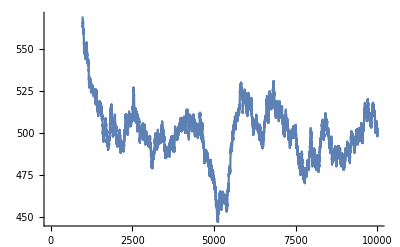

```mathematica
nl=n;
nllist={nl};
For[itime=1,itime≤tmax,itime++,
prob=nl/n;
rnd=RandomReal[];
If[rnd≤prob,nl=nl-1,nl=nl+1];
AppendTo[nllist,nl]
]
ListLinePlot[nllist]
```